## Load Radia

```mathematica
<<Radia`;
RadPlot3DOptions[];
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

## Load Insertion Device Functions

Open and evaluate the notebook “IDFunctions.nb”

## Set Directory

```mathematica
SetDirectory["C:\\Users\\luana.vilela\\lnls-ima\\id-sabia\\simulation\\magnetic"];
```

## Parameters

```mathematica
(*ID parameters*)
λu = 52.5; (*Period [mm]*)
Np = 44; (*Number of periods (not including terminations)*)
Br = 1.37; (*Remanent magnetization [T]*)
gap = 13.6;
BlockGap = 0.125;
BlockVersion = "ERred" ;
BlockScale= 1;
Termination = "ThreeBlocksAntiSym"; 

(*Longitudinal range [mm]*)
Lstep = 0.1;
Li = -1500;
Lf = 1500;
Lnpts =Round[(Lf - Li)/Lstep ]+ 1; 

(*Horizontal range [mm]*)
Hstep =1;
Hi = -1;
Hf = 1;
Hnpts = Round[(Hf - Hi)/Hstep ]+ 1; 

(*Vertical range [mm]*)
Vstep =0.45;
Vi = -3.6;
Vf = 3.6;
Vnpts = Round[(Vf - Vi)/Vstep ]+ 1; 

(*Particle energy [GeV]*)
Energy = 3;

(*Radia randomization magnitudes*)
radFldLenTol[10^-12,10^-12 ];

idname="id_sabia";
```

## Fieldmap δP 0

δP  [mm]: 0

δGV [mm]: 0

δGH [mm]: 0

δCP [mm]: 0

IDDelta: elapsed time = 1.546871 s

IDShow: elapsed time = 2.57812 s

Horizontal field amplitude:    2.53312×10^-8 [T]

Vertical field amplitude:      1.25619 [T]

Longitudinal field amplitude:  4.96803×10^-10 [T]

Horizontal K: 6.15973

Vertical K:   1.24212×10^-7

IDInfo: elapsed time = 1.093752 s

IDPlotFields: elapsed time = 35.218652 s

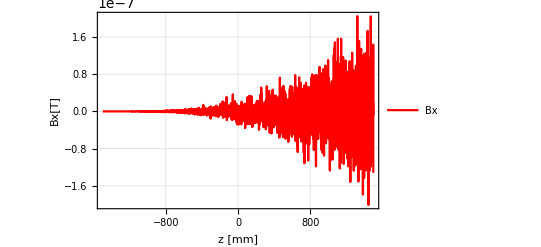
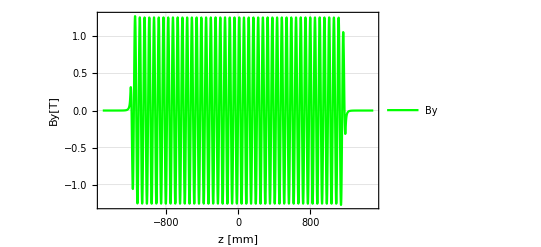
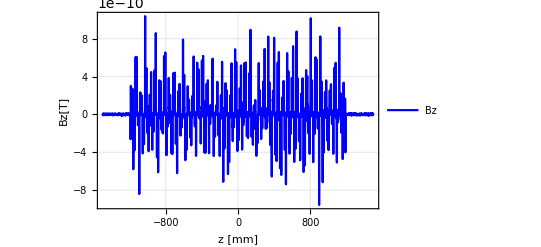

```mathematica
δP = 0;
δGV = 0;
δGH = 0;
δCP = 0;
Print["δP  [mm]: ",  δP];
Print["δGV [mm]: ",  δGV];
Print["δGH [mm]: ",  δGH];
Print["δCP [mm]: ",  δCP];

fieldmapfilename = StringTemplate["`1`_fieldmap_dP_`2`_dGV_`3`_dGH_`4`_dCP_`5`.txt"][idname, δP, δGV, δGH, δCP];
kickmapfilename = StringTemplate["`1`_kickmap_dP_`2`_dGV_`3`_dGH_`4`_dCP_`5`.txt"][idname, δP, δGV, δGH, δCP];

ID= IDDelta[λu, Np, Br, gap, "δP" -> δP, "δGV"-> δGV, "δGH"-> δGH,"δCP"-> δCP,"BlockGap"-> BlockGap,"BlockVersion"-> BlockVersion, "BlockScale"-> BlockScale,"Termination" -> Termination];
IDShow[ID]
IDInfo[ID, λu]
IDPlotFields[ID, "z", {Li, Lf}]
```

```mathematica
IDSeg =radObjDivMag[ID , {{3,1},{3,1},{3,1}}];
IDShow[IDSeg]
```

```mathematica
Mat= radMatLin[{0.05,0.15},Br];
IDMat = radMatApl[IDSeg, Mat];
```

```mathematica
t0=AbsoluteTime[];
sre=RadSolve[IDMat,0.00000001,100000];
t1=AbsoluteTime[];
sz = radObjDegFre[IDMat];

Print["Solved in: ",Round[t1-t0]/60.0," min"];
Print["Number of Degrees of Freedom = ",sz];
Print["Typical Memory Size of Interation Matrix [MBytes] = ",N[sz*(sz+1)*4/1000000]]; 
Print["Average absolute change in magnetization between the last two iterations = ",sre[[1]]];
Print["Maximum absolute value of magnetization over all the objects = ",sre[[2]]];
Print["Maximum absolute value of magnetic field strength over central points of all the objects = ",sre[[3]]];
Print["Number of iterations done = ",sre[[4]], "\n"];
```

Solved in: 36.35 min

Number of Degrees of Freedom = 118584

Typical Memory Size of Interation Matrix [MBytes] = 56249.1

Average absolute change in magnetization between the last two iterations = 1.62551×10^-9

Maximum absolute value of magnetization over all the objects = 1.39274

Maximum absolute value of magnetic field strength over central points of all the objects = 1.40863

Number of iterations done = 5

IDShow: elapsed time = 17.218726 s

Horizontal field amplitude:    6.25601×10^-8 [T]

Vertical field amplitude:      1.22508 [T]

Longitudinal field amplitude:  9.44292×10^-10 [T]

Horizontal K: 6.00716

Vertical K:   3.06764×10^-7

IDInfo: elapsed time = 13.796868 s

IDPlotFields: elapsed time = 429.0015535 s

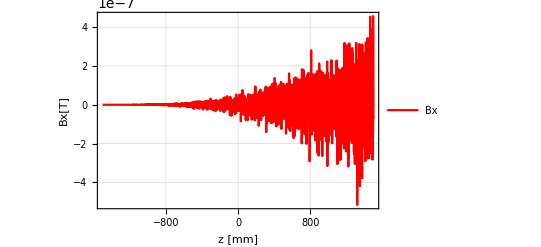
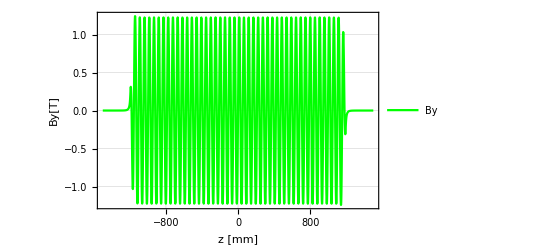
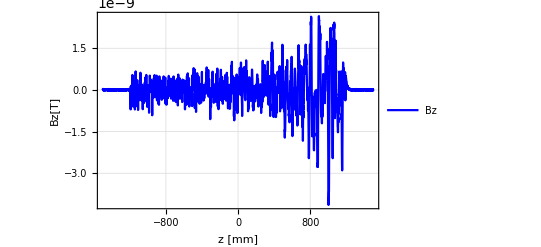

```mathematica
IDShow[IDMat]
IDInfo[IDMat, λu]
IDPlotFields[IDMat, "z", {Li, Lf}]
```

```mathematica
IDFieldMap[fieldmapfilename, IDMat, {Hi, Hf}, {0, 0}, {Li,Lf}, Hnpts, 1, Lnpts ] ;
```

Fieldmap saved in file: ERred_fieldmap_dP_0_dGV_0_dGH_0_dCP_0.txt

IDFieldMap: elapsed time = 3722.350942 s

## Fieldmap δP 0, step = 0.1mm

δP  [mm]: 0

δGV [mm]: 0

δGH [mm]: 0

δCP [mm]: 0

IDDelta: elapsed time = 1.640639 s

Solved in: 35.3833 min

Number of Degrees of Freedom = 118584

Typical Memory Size of Interation Matrix [MBytes] = 56249.1

Average absolute change in magnetization between the last two iterations = 1.62276×10^-9

Maximum absolute value of magnetization over all the objects = 1.39274

Maximum absolute value of magnetic field strength over central points of all the objects = 1.40863

Number of iterations done = 5

IDShow: elapsed time = 18.156225 s

Horizontal field amplitude:    6.1061×10^-8 [T]

Vertical field amplitude:      1.22508 [T]

Longitudinal field amplitude:  9.9705×10^-10 [T]

Horizontal K: 6.00716

Vertical K:   2.99413×10^-7

IDInfo: elapsed time = 13.718712 s

IDPlotFields: elapsed time = 417.6863773 s

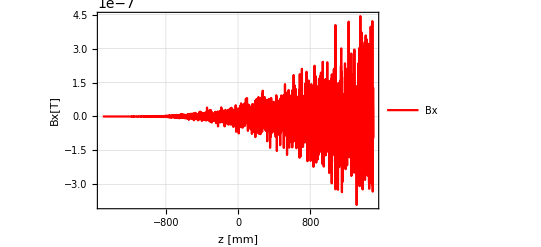
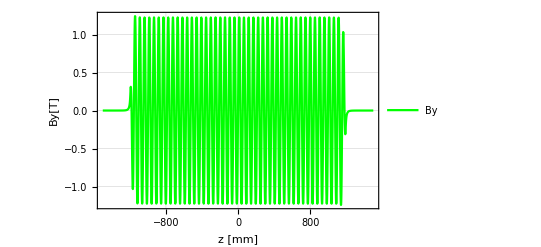
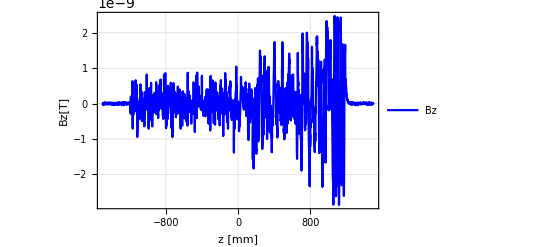

Fieldmap saved in file: id_sabia_fieldmap_dP_0_dGV_0_dGH_0_dCP_0.txt

IDFieldMap: elapsed time = 4222.8836159 s

```mathematica
δP = 0;
δGV = 0;
δGH = 0;
δCP = 0;
Print["δP  [mm]: ",  δP];
Print["δGV [mm]: ",  δGV];
Print["δGH [mm]: ",  δGH];
Print["δCP [mm]: ",  δCP];

fieldmapfilename = StringTemplate["`1`_fieldmap_dP_`2`_dGV_`3`_dGH_`4`_dCP_`5`.txt"][idname, δP, δGV, δGH, δCP];
kickmapfilename = StringTemplate["`1`_kickmap_dP_`2`_dGV_`3`_dGH_`4`_dCP_`5`.txt"][idname, δP, δGV, δGH, δCP];

ID= IDDelta[λu, Np, Br, gap, "δP" -> δP, "δGV"-> δGV, "δGH"-> δGH,"δCP"-> δCP,"BlockGap"-> BlockGap,"BlockVersion"-> BlockVersion, "BlockScale"-> BlockScale,"Termination" -> Termination];

IDSeg =radObjDivMag[ID , {{3,1},{3,1},{3,1}}];

Mat= radMatLin[{0.05,0.15},Br];
IDMat = radMatApl[IDSeg, Mat];

t0=AbsoluteTime[];
sre=RadSolve[IDMat,0.00000001,100000];
t1=AbsoluteTime[];
sz = radObjDegFre[IDMat];

Print["Solved in: ",Round[t1-t0]/60.0," min"];
Print["Number of Degrees of Freedom = ",sz];
Print["Typical Memory Size of Interation Matrix [MBytes] = ",N[sz*(sz+1)*4/1000000]]; 
Print["Average absolute change in magnetization between the last two iterations = ",sre[[1]]];
Print["Maximum absolute value of magnetization over all the objects = ",sre[[2]]];
Print["Maximum absolute value of magnetic field strength over central points of all the objects = ",sre[[3]]];
Print["Number of iterations done = ",sre[[4]], "\n"];

IDShow[IDMat]
IDInfo[IDMat, λu]
IDPlotFields[IDMat, "z", {Li, Lf}]

IDFieldMap[fieldmapfilename, IDMat, {Hi, Hf}, {0, 0}, {Li,Lf}, Hnpts, 1, Lnpts ] ;
```

## Fieldmap δP λu/4

δP  [mm]: 13.125

δGV [mm]: 0

δGH [mm]: 0

δCP [mm]: 0

IDDelta: elapsed time = 1.593743 s

IDShow: elapsed time = 2.593744 s

Horizontal field amplitude:    0.899058 [T]

Vertical field amplitude:      0.899329 [T]

Longitudinal field amplitude:  6.53296×10^-10 [T]

Horizontal K: 4.40986

Vertical K:   4.40853

IDInfo: elapsed time = 1.093747 s

IDPlotFields: elapsed time = 33.953027 s

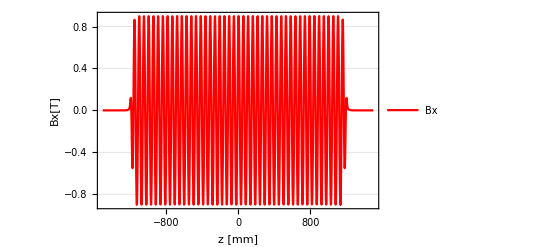
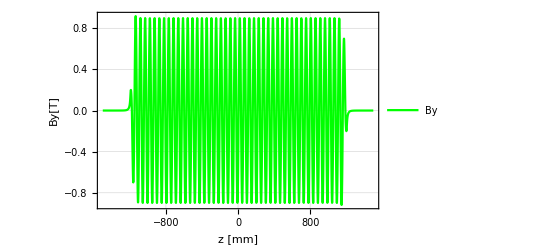
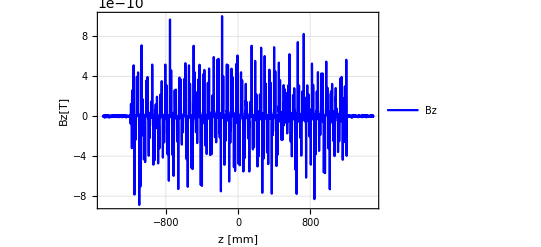

```mathematica
δP = λu/4;
δGV = 0;
δGH = 0;
δCP = 0;
Print["δP  [mm]: ",  δP];
Print["δGV [mm]: ",  δGV];
Print["δGH [mm]: ",  δGH];
Print["δCP [mm]: ",  δCP];

fieldmapfilename = StringTemplate["`1`_fieldmap_dP_`2`_dGV_`3`_dGH_`4`_dCP_`5`.txt"][idname, δP, δGV, δGH, δCP];
kickmapfilename = StringTemplate["`1`_kickmap_dP_`2`_dGV_`3`_dGH_`4`_dCP_`5`.txt"][idname, δP, δGV, δGH, δCP];

ID= IDDelta[λu, Np, Br, gap, "δP" -> δP, "δGV"-> δGV, "δGH"-> δGH,"δCP"-> δCP,"BlockGap"-> BlockGap,"BlockVersion"-> BlockVersion, "BlockScale"-> BlockScale,"Termination" -> Termination];
IDShow[ID]
IDInfo[ID, λu]
IDPlotFields[ID, "z", {Li, Lf}]
```

```mathematica
IDSeg =radObjDivMag[ID , {{3,1},{3,1},{3,1}}];
IDShow[IDSeg]
```

```mathematica
Mat= radMatLin[{0.05,0.15},Br];
IDMat = radMatApl[IDSeg, Mat];
```

```mathematica
t0=AbsoluteTime[];
sre=RadSolve[IDMat,0.00000001,100000];
t1=AbsoluteTime[];
sz = radObjDegFre[IDMat];

Print["Solved in: ",Round[t1-t0]/60.0," min"];
Print["Number of Degrees of Freedom = ",sz];
Print["Typical Memory Size of Interation Matrix [MBytes] = ",N[sz*(sz+1)*4/1000000]]; 
Print["Average absolute change in magnetization between the last two iterations = ",sre[[1]]];
Print["Maximum absolute value of magnetization over all the objects = ",sre[[2]]];
Print["Maximum absolute value of magnetic field strength over central points of all the objects = ",sre[[3]]];
Print["Number of iterations done = ",sre[[4]], "\n"];
```

Solved in: 36.6833 min

Number of Degrees of Freedom = 118584

Typical Memory Size of Interation Matrix [MBytes] = 56249.1

Average absolute change in magnetization between the last two iterations = 1.7342×10^-9

Maximum absolute value of magnetization over all the objects = 1.38719

Maximum absolute value of magnetic field strength over central points of all the objects = 1.43874

Number of iterations done = 5

IDShow: elapsed time = 17.671851 s

Horizontal field amplitude:    0.874309 [T]

Vertical field amplitude:      0.874572 [T]

Longitudinal field amplitude:  1.09164×10^-9 [T]

Horizontal K: 4.28846

Vertical K:   4.28717

IDInfo: elapsed time = 14.01558 s

IDPlotFields: elapsed time = 418.5457775 s

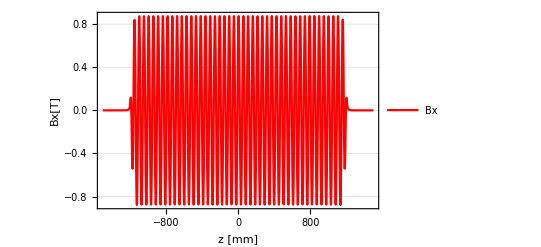
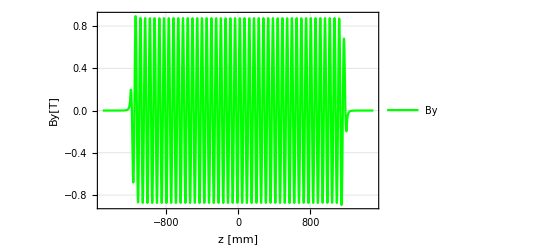
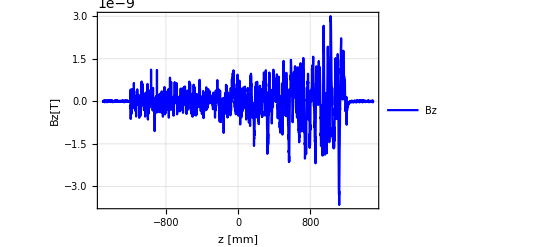

```mathematica
IDShow[IDMat]
IDInfo[IDMat, λu]
IDPlotFields[IDMat, "z", {Li, Lf}]
```

```mathematica
IDFieldMap[fieldmapfilename, IDMat, {Hi, Hf}, {0, 0}, {Li,Lf}, Hnpts, 1, Lnpts ] ;
```

Fieldmap saved in file: ERred_fieldmap_dP_13.125_dGV_0_dGH_0_dCP_0.txt

IDFieldMap: elapsed time = 3745.1480344 s